# Misure ripetute Gaussian Occurences

## Istogrammi di misure ripetute Histograms of Repeated Measures

# Istruzioni Instructions

Il foglio di Mathematica analizza un foglio contenente dati di misure ripetute e restituisce parametri come il chi quadro della distribuzione. L’analisi si svolge in due sezioni separate: nella prima si assume una distribuzione normale di probabilità, mentre nella seconda una distribuzione di Poisson. Il file di dati passato al programma può contenere anche un’eventuale riga d’intestazione che verrà automaticamente ignorata dal programma. Si suppone che la distribuzione seguita dal singolo conteggio sia del tipo di Poisson (errore pari alla radice quadrata del conteggio stesso).
L’output del foglio di calcolo è visibile aprendo le celle corrispondenti, ma è anche reperibile nella carte “Documenti” dell’utente. Vengono salvati grafici e analisi dati come file di immagine e fogli di calcolo .xls.

Per info:
Riccardo Finotello
riccardo.finotello@edu.unito.it

This Mathematica notebook performs repeated measures analysis and return several parameters of the distribution. The analysis is performed in two steps: during the first a normal distribution is used, while during the second a Poisson distribution. The input file may contain a title line, which will be automatically ignored. During the Poisson analysis, error on the counts is the square root.
Results will be inserted in a separate file, inside the “Documents” directory as images and .xls.

# Input dei dati Data input

```mathematica
Clear["Global`*"] (* restting notebook *)
Needs["ErrorBarPlots`"](* error bars package *)
```

```mathematica
NomeEsperienza="AAA";(* name of the main directory: avoid spaces *)
NomeFit="EnergiaFit";(* name of the subdirectory: avoid spaces *)
InputFile="Desktop\\EnergiaFit.dat";(* insert path to file: \\ or / to separate *)
EtichettaAscissa="E" ; (* ascissae label *)
UnitàMisuraAscissa="MeV";(* unit of measure for the ascissae: insert _ or Blank[] if not needed *)
EtichettaOrdinata="#";(* ordinata label *)
UnitàMisuraOrdinata=_;(* unit of measure for the ordinata: insert _ or Blank[] if not needed *)
AmpiezzaClassiIniziale=2; (* first bin width: usually the sensibility of the instrument*)
AmpiezzaClassiRielaborazione = 3; (* more accurate bin width *)
```

# Analisi dei dati Data Analysis

### Input del file indicato Inputting the file

```mathematica
inputData=Import[InputFile,"Data"];
```

### Costruzione liste di valori e frequenze Values and frequences list

```mathematica
If[StringQ[inputData[[1,1]]],counts=Drop[Flatten[inputData[[All,1]]],1],counts=Flatten[inputData[[All,1]]]];
```

```mathematica
TopLimit=50;
If[Length[counts]≤TopLimit,Print["y = ",counts],"Lists are too long to be shown"]
```

y = {0.16,0.18,0.2,0.22}

### Grafico della distribuzione Histogram of the distribution

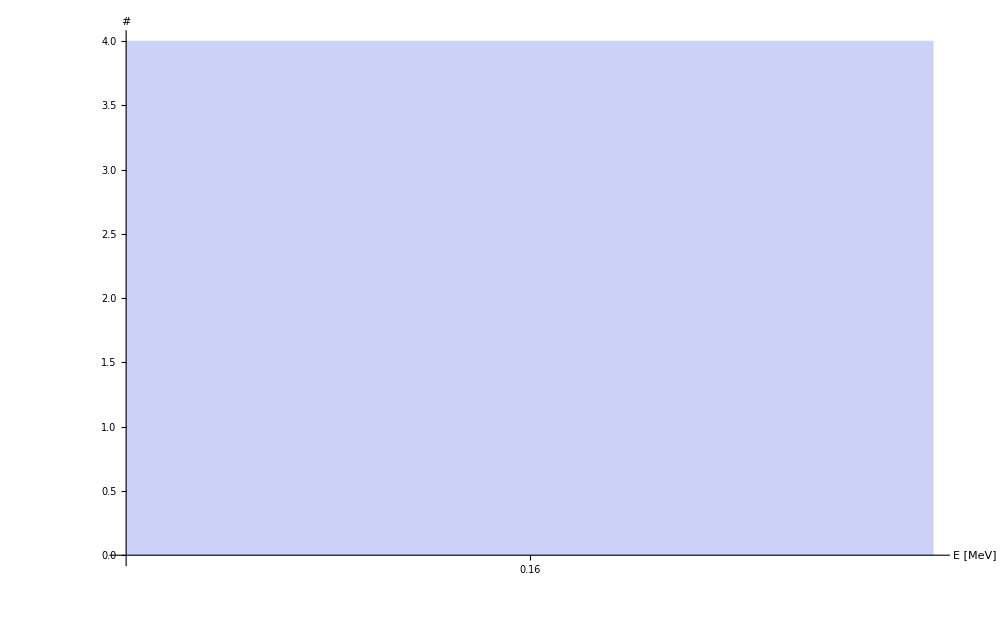

```mathematica
If[StringQ[UnitàMisuraAscissa],AscissaLabel=EtichettaAscissa<>" ["<>UnitàMisuraAscissa<>"]",AscissaLabel=EtichettaAscissa];
If[StringQ[UnitàMisuraOrdinata],OrdinataLabel=EtichettaOrdinata<>" ["<>UnitàMisuraOrdinata<>"]",OrdinataLabel=EtichettaOrdinata];
Frequenze=BinCounts[counts,{Min[counts]-AmpiezzaClassiIniziale/2,Max[counts]+AmpiezzaClassiIniziale/2,AmpiezzaClassiIniziale}];
Punti1=Table[i,{i,Min[counts],Max[counts],AmpiezzaClassiIniziale}];
Istogramma1=Histogram[counts,{Min[counts]-AmpiezzaClassiIniziale/2,Max[counts]+AmpiezzaClassiIniziale/2,AmpiezzaClassiIniziale},"Count",ImageSize->1000,Ticks->{Punti1,Automatic},AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Bold,Black,Large]]
```

### Grafico dei punti con gli errori Error plot

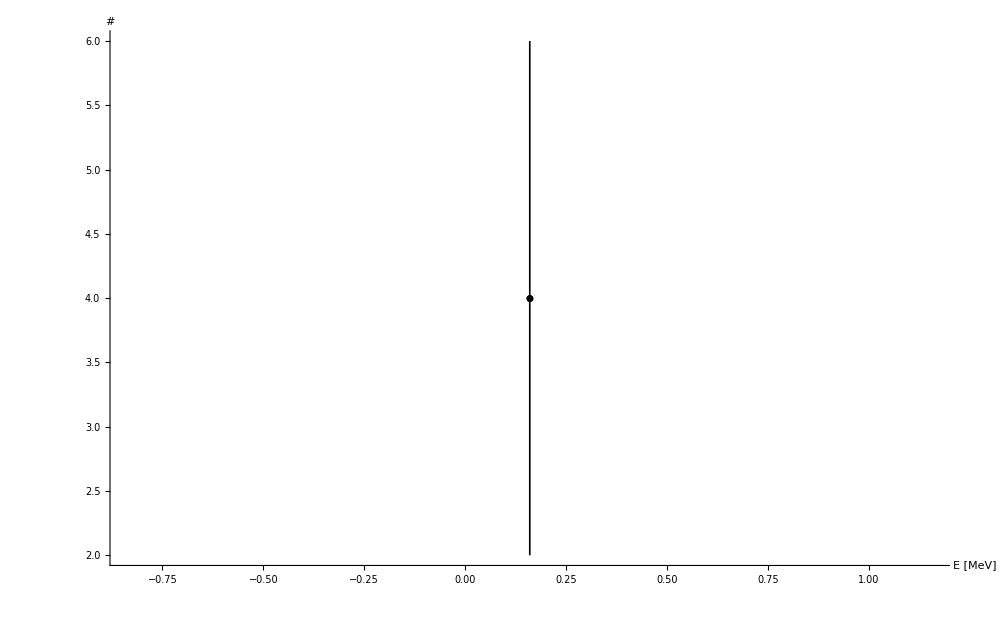

```mathematica
err=Table[{{Punti1[[i]],Frequenze[[i]]},ErrorBar[Sqrt[Frequenze[[i]]]]},{i,1,Length[Punti1]}];
ErrorPlot=ErrorListPlot[err,PlotRange->All,PlotMarkers->Automatic,PlotStyle->Black,ImageSize->1000,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Bold,Black,Large]]
```

### Creazione dei grafici (distribuzione gaussiana) Gaussian distribution

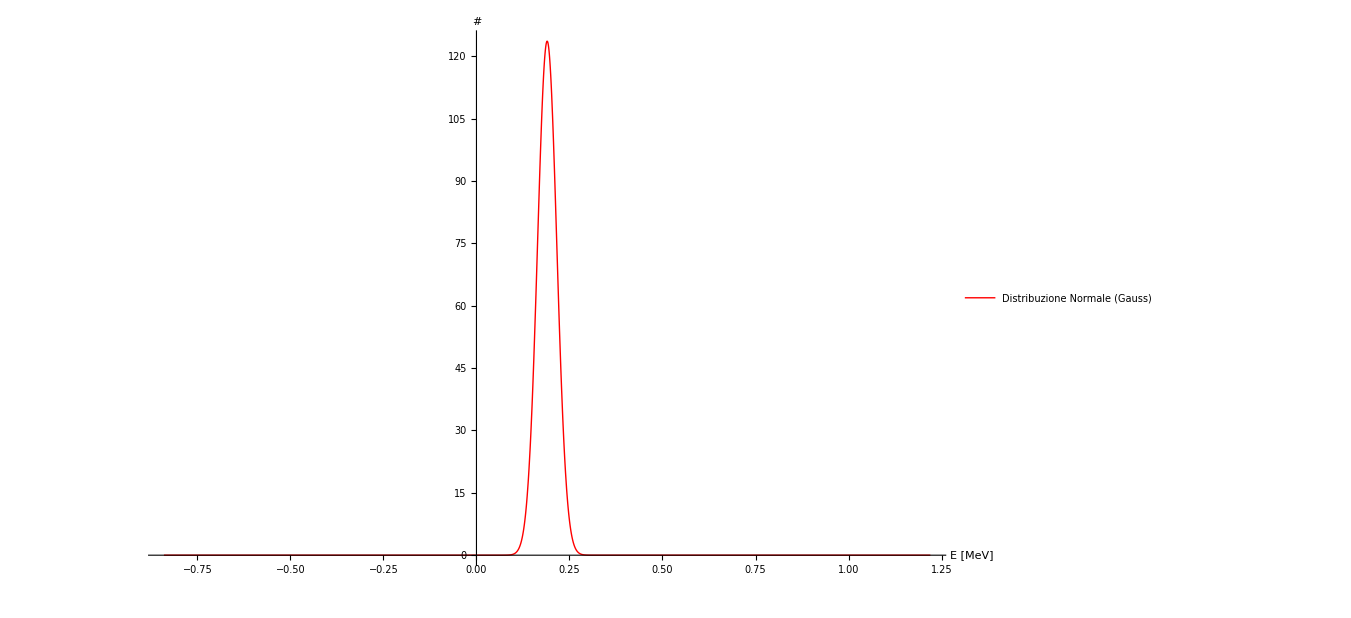

```mathematica
Gaussiana1[x_]:=Length[counts]*AmpiezzaClassiIniziale*PDF[NormalDistribution[Mean[counts],StandardDeviation[counts]],x];
GraficoGaussiana1=Plot[Gaussiana1[x],{x,Min[counts]-AmpiezzaClassiIniziale/2,Max[counts]+AmpiezzaClassiIniziale/2},PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},ImageSize->1000,LabelStyle->Directive[Bold,Black,Large],PlotStyle->Red,PlotLegends->{"Distribuzione Normale (Gauss)"}]
```

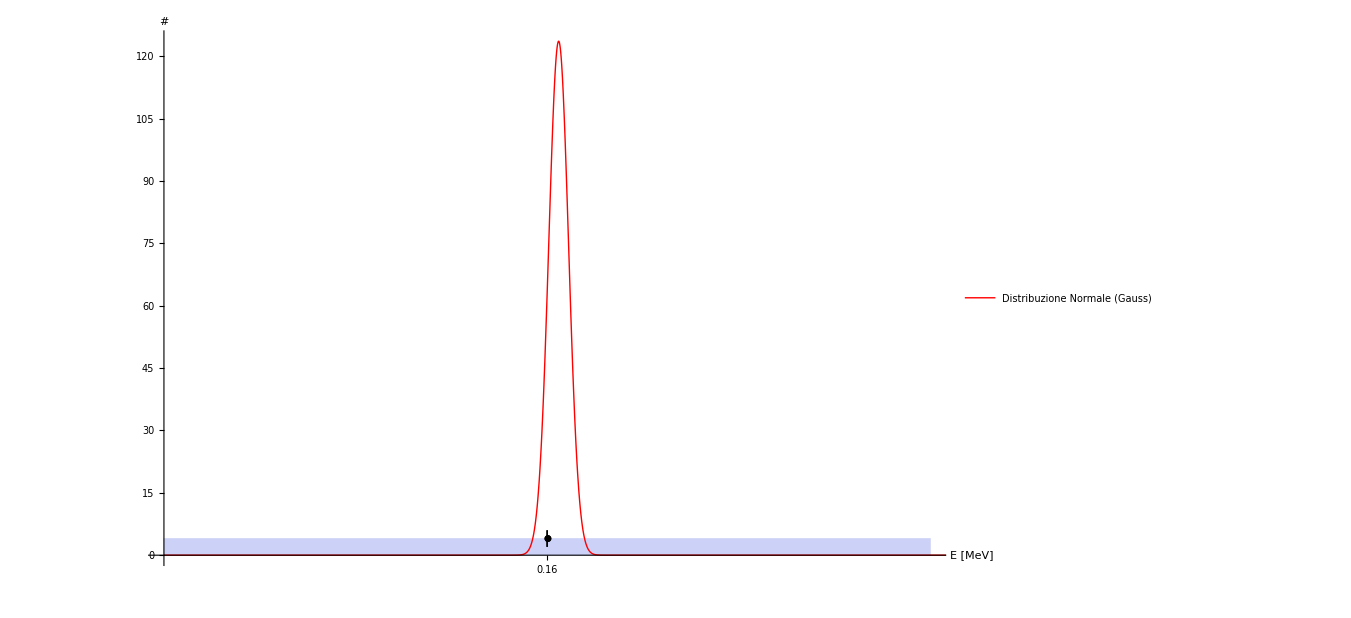

```mathematica
GraficoGaussianaDistribuzione1=Show[Istogramma1,GraficoGaussiana1,ErrorPlot]
```

### Dati entro il 3-sigma 3-sigma data

```mathematica
bound1=Mean[counts]-3*StandardDeviation[counts];
bound2=Mean[counts]+3*StandardDeviation[counts];
countsTreSigma=Select[Sort[counts],bound1≤#≤bound2&];
FrequenzeTreSigma=BinCounts[countsTreSigma,{Min[countsTreSigma]-AmpiezzaClassiIniziale/2,Max[countsTreSigma]+AmpiezzaClassiIniziale/2,AmpiezzaClassiIniziale}];
Istogramma2=Histogram[countsTreSigma,{Min[countsTreSigma]-AmpiezzaClassiIniziale/2,Max[countsTreSigma]+AmpiezzaClassiIniziale/2,AmpiezzaClassiIniziale},"Count",ImageSize->1000,Ticks->{Punti1,Automatic},AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Bold,Black]]
```

-Graphics-

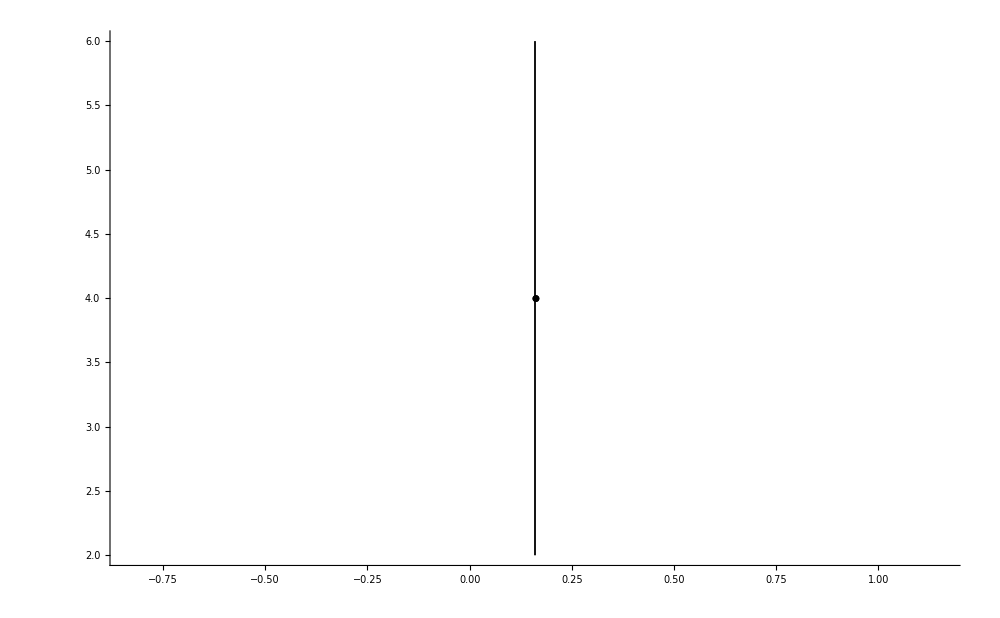

```mathematica
err=Table[{{Punti1[[i]],FrequenzeTreSigma[[i]]},ErrorBar[Sqrt[FrequenzeTreSigma[[i]]]]},{i,1,Length[Punti1]}];
ErrorPlot2=ErrorListPlot[err,PlotRange->All,PlotMarkers->Automatic,PlotStyle->Black,ImageSize->1000]
```

```mathematica
Gaussiana2[x_]:=Length[countsTreSigma]*AmpiezzaClassiIniziale*PDF[NormalDistribution[Mean[counts],StandardDeviation[counts]],x];
GraficoGaussiana2=Plot[Gaussiana2[x],{x,Min[countsTreSigma]-AmpiezzaClassiIniziale/2,Max[countsTreSigma]+AmpiezzaClassiIniziale/2},PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},ImageSize->1000,LabelStyle->Directive[Bold,Black],PlotStyle->Red,PlotLegends->{"Distribuzione Normale (Gauss)"}]
```

-Graphics-

```mathematica
GraficoGaussianaDistribuzione2=Show[Istogramma2,GraficoGaussiana2,ErrorPlot2]
```

-Graphics-

### Dati a classi raggruppate Refined bin width

```mathematica
FrequenzeClassiRaggruppate=BinCounts[countsTreSigma,{Min[countsTreSigma]-AmpiezzaClassiRielaborazione/2,Max[countsTreSigma]+AmpiezzaClassiRielaborazione/2,AmpiezzaClassiRielaborazione}];
Punti2=Table[i,{i,Min[countsTreSigma],Max[countsTreSigma],AmpiezzaClassiRielaborazione}];
MediaClassiRaggruppate=(Total[FrequenzeClassiRaggruppate*Punti2])/(Length[countsTreSigma]);
DeviazioneClassiRaggruppate=Sqrt[Total[((Punti2-MediaClassiRaggruppate)^2)*FrequenzeClassiRaggruppate]/(Length[countsTreSigma]-1)];
Istogramma3=Histogram[countsTreSigma,{Min[countsTreSigma]-AmpiezzaClassiRielaborazione/2,Max[countsTreSigma]+AmpiezzaClassiRielaborazione/2,AmpiezzaClassiRielaborazione},"Count",ImageSize->1000,Ticks->{Punti2,Automatic},AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Bold,Black]]
```

-Graphics-

### Grafico dei punti con gli errori Error plot

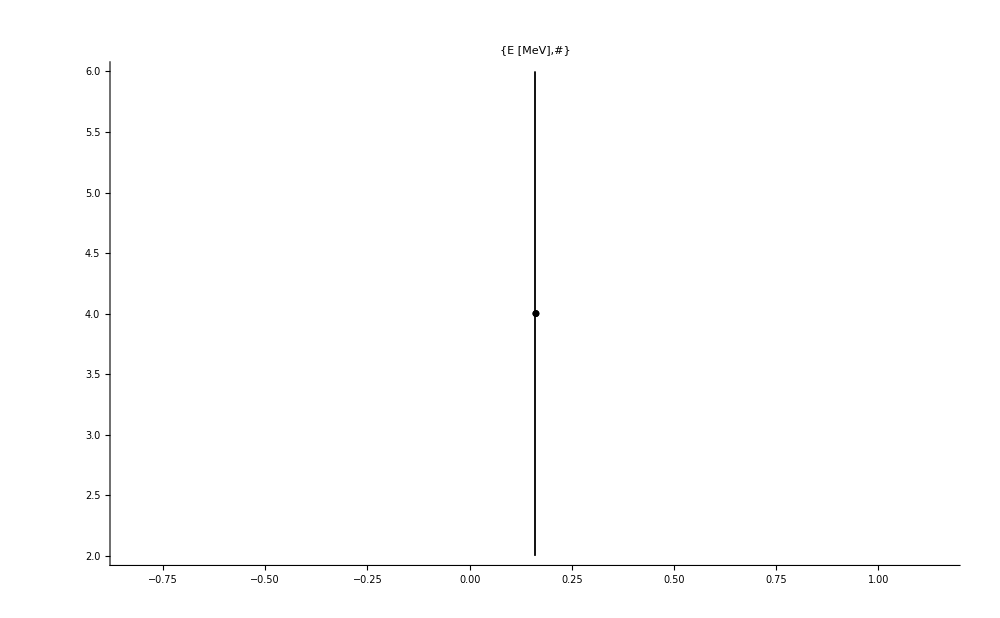

```mathematica
err=Table[{{Punti2[[i]],FrequenzeClassiRaggruppate[[i]]},ErrorBar[Sqrt[FrequenzeClassiRaggruppate[[i]]]]},{i,1,Length[Punti2]}];
ErrorPlot3=ErrorListPlot[err,PlotRange->All,PlotMarkers->Automatic,PlotStyle->Black,PlotLabel->{AscissaLabel,OrdinataLabel},ImageSize->1000]
```

```mathematica
Gaussiana3[x_]:=Length[countsTreSigma]*AmpiezzaClassiRielaborazione*PDF[NormalDistribution[MediaClassiRaggruppate,DeviazioneClassiRaggruppate],x];
GraficoGaussiana3=Plot[Gaussiana3[x],{x,Min[countsTreSigma]-AmpiezzaClassiRielaborazione/2,Max[countsTreSigma]+AmpiezzaClassiRielaborazione/2},PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},ImageSize->1000,LabelStyle->Directive[Bold,Black],PlotStyle->Red,PlotLegends->{"Distribuzione Normale (Gauss)"}]
```

NormalDistribution::posprm: Parameter 0. at position 2 in NormalDistribution[0.16, 0.] is expected to be positive.

General::stop: Further output of NormalDistribution :: posprm will be suppressed during this calculation.

-Graphics-

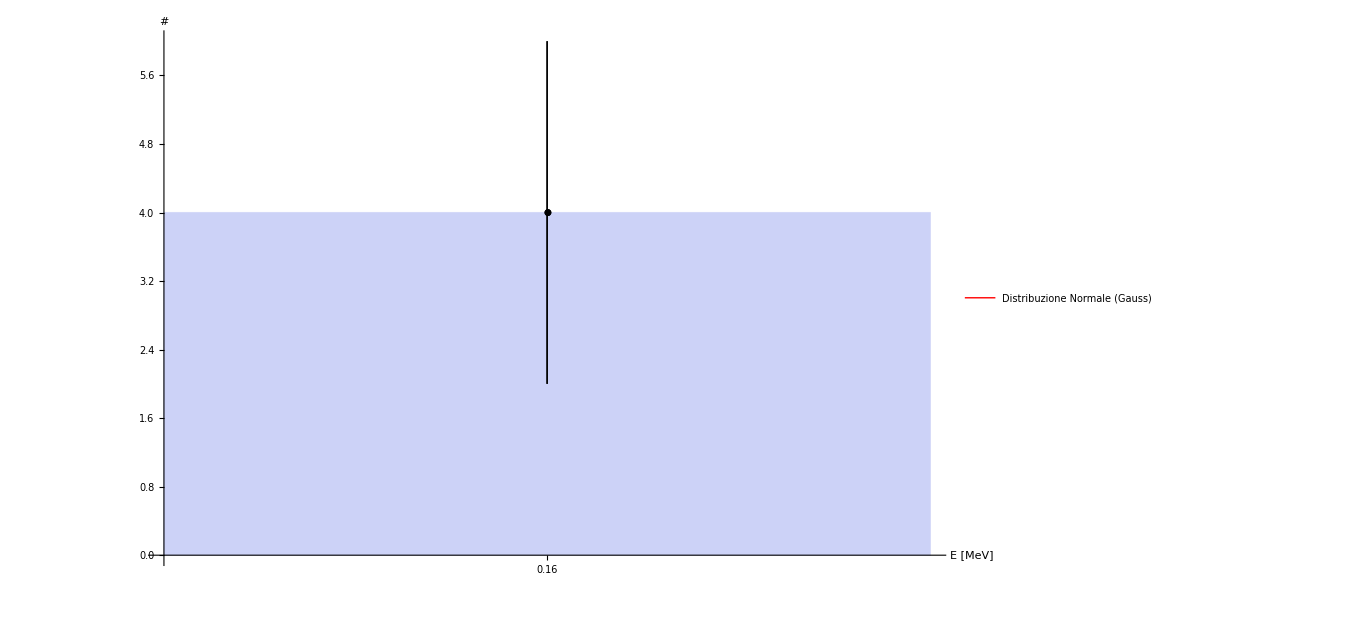

```mathematica
GraficoGaussianaDistribuzione3=Show[Istogramma3,GraficoGaussiana3,ErrorPlot3]
```

### Analisi delle distribuzioni gaussiane (dati entro 3-sigma, classi raggruppate e non) Gaussian analysis (data inside 3-sigma interval, raw and refined bin width)

```mathematica
(* Classes with frequency less than 5 are grouped *)
GaussExpected1=Length[countsTreSigma]*AmpiezzaClassiIniziale*PDF[NormalDistribution[Mean[countsTreSigma],StandardDeviation[countsTreSigma]],Punti1];
GaussExpected2=Length[countsTreSigma]*AmpiezzaClassiRielaborazione*PDF[NormalDistribution[Mean[countsTreSigma],StandardDeviation[countsTreSigma]],Punti2];
```

```mathematica
(* Non grouped classes *)
GaussExpected1Coda1=Take[GaussExpected1,Length[GaussExpected1]/2];
Ek1Buff1=Select[GaussExpected1Coda1,#≤5&];
GaussExpected1Coda2=Drop[GaussExpected1,Length[GaussExpected1]/2];
Ek1Buff2=Select[GaussExpected1Coda2,#≤5&];
Ek1=Join[{Total[Ek1Buff1]},Take[GaussExpected1,{Length[Ek1Buff1],Length[FrequenzeTreSigma]-Length[Ek1Buff2]}],{Total[Ek1Buff2]}];
Ok1=Join[{Total[Take[FrequenzeTreSigma,Length[Ek1Buff1]]]},Take[FrequenzeTreSigma,{Length[Ek1Buff1],Length[FrequenzeTreSigma]-Length[Ek1Buff2]}],{Total[Take[FrequenzeTreSigma,-Length[Ek1Buff2]]]}];
Chi21=N[Total[((Ok1-Ek1)^2)/Ek1]];
dof1=Length[Ek1]-3;
Print["χ^2 = ", Chi21]
Print["Degrees of freedom: dof = ",dof1]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{62.9357}, 1/2].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{62.9357}, 1/2].

Total::normal: Nonatomic expression expected at position 1 in Total[1/2].

Total::normal: Nonatomic expression expected at position 1 in Total[0.5].

χ^2 = 2. Total[0.5]

Gradi di libertà: dof = -1

```mathematica
(* Grouped classes *)
GaussExpected2Coda1=Take[GaussExpected2,Length[GaussExpected2]/2];
Ek2Buff1=Select[GaussExpected2Coda1,#≤5&];
GaussExpected2Coda2=Drop[GaussExpected2,Length[GaussExpected2]/2];
Ek2Buff2=Select[GaussExpected2Coda2,#≤5&];
Ek2=Join[{Total[Ek2Buff1]},Take[GaussExpected2,{Length[Ek2Buff1],Length[FrequenzeClassiRaggruppate]-Length[Ek2Buff2]}],{Total[Ek2Buff2]}];
Ok2=Join[{Total[Take[FrequenzeClassiRaggruppate,Length[Ek2Buff1]]]},Take[FrequenzeClassiRaggruppate,{Length[Ek2Buff1],Length[FrequenzeClassiRaggruppate]-Length[Ek2Buff2]}],{Total[Take[FrequenzeClassiRaggruppate,-Length[Ek2Buff2]]]}];
Chi22=N[Total[((Ok2-Ek2)^2)/Ek2]];
dof2=Length[Ek2]-3;
Print["χ^2 = ", Chi22]
Print["Degrees of freedom: dof = ",dof2]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{94.4035}, 1/2].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{94.4035}, 1/2].

Total::normal: Nonatomic expression expected at position 1 in Total[1/2].

Total::normal: Nonatomic expression expected at position 1 in Total[0.5].

χ^2 = 2. Total[0.5]

Gradi di libertà: dof = -1

# Export su file File export

```mathematica
dir=$UserDocumentsDirectory<>"\\"<>NomeEsperienza<>"\\"<>NomeFit;
CreateDirectory[dir];
```

CreateDirectory::filex: "C:\\Users\\ricca_000\\Documents\\AAA\\EnergiaFit\\" already exists.

```mathematica
If[DirectoryQ[dir<>"\\Gauss"],primaAnalisi=SetDirectory[dir<>"\\Gauss"],primaAnalisi=CreateDirectory[dir<>"\\Gauss"]];
SetDirectory[dir];
Print["Files will be saved in: ",dir]
```

I file verranno inseriti nelle cartelle corrispondenti al seguente indirizzo: C:\Users\ricca_000\Documents\AAA\EnergiaFit

#### Export dei contenuti della analisi gaussiana

```mathematica
outputGauss={{,"Data analysis (Gauss)",},{,,},{,"Raw data",},{"Mean = ",Mean[counts],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa,""]},{"Sigma = ",StandardDeviation[counts],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa,""]},{,,},{,"Data in 3-sigma",},{"Mean = ",Mean[countsTreSigma],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa,""]},{"Sigma = ",StandardDeviation[countsTreSigma],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa,""]},{"Chi Square: ",Chi21,},{"Degrees of freedom: ",dof1,},{,,},{,"Refined bin width",},{"Mean = ",MediaClassiRaggruppate,If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa,""]},{"Sigma = ",DeviazioneClassiRaggruppate,If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa,""]},{"Chi Square: ",Chi22,},{"Degrees of freedom: ",dof2,}};
CreateDirectory[primaAnalisi<>"\\MisureRipetute"];
CreateDirectory[primaAnalisi<>"\\TreSigma"];
CreateDirectory[primaAnalisi<>"\\ClassiRaggruppate"];
SetDirectory[dir];
Export[file1=primaAnalisi<>"\\AnalisiDati.xls",outputGauss];
Export[graph1=primaAnalisi<>"\\MisureRipetute\\Istogramma.png",Istogramma1];
Export[graph2=primaAnalisi<>"\\MisureRipetute\\Gaussiana.png",GraficoGaussiana1];
Export[graph3=primaAnalisi<>"\\MisureRipetute\\Distribuzione.png",GraficoGaussianaDistribuzione1];
Export[graph4=primaAnalisi<>"\\MisureRipetute\\Completo.png",ErrorPlot];
Export[graph5=primaAnalisi<>"\\TreSigma\\Istogramma.png",Istogramma2];
Export[graph6=primaAnalisi<>"\\TreSigma\\Gaussiana.png",GraficoGaussiana2];
Export[graph7=primaAnalisi<>"\\TreSigma\\Distribuzione.png",GraficoGaussianaDistribuzione2];
Export[graph8=primaAnalisi<>"\\MisureRipetute\\Completo.png",ErrorPlot2];
Export[graph9=primaAnalisi<>"\\ClassiRaggruppate\\Istogramma.png",Istogramma3];
Export[graph10=primaAnalisi<>"\\ClassiRaggruppate\\Gaussiana.png",GraficoGaussiana3];
Export[graph11=primaAnalisi<>"\\ClassiRaggruppate\\Distribuzione.png",GraficoGaussianaDistribuzione3];
Export[graph12=primaAnalisi<>"\\MisureRipetute\\Completo.png",ErrorPlot3];
```